# 1. Motivation: the population of merger product candidates in Gaia’s complete 100 pc sample

Here we provide the main motivations for our study. Motivations relate to the properties of white dwarfs in the complete volume limited 100 pc sample. Our main motivation is the Ultra-massive white dwarfs which have been identified as candidate double white dwarf merger products.

### a. The mass distribution of white dwarfs in the 100 pc sample

```mathematica
SetDirectory["/Users/lucym/Documents/2026/Maria-visit"]
```

/Users/lucym/Documents/2026/Maria-visit

```mathematica
FilenameQ = "DQ-1.dat";
FilenameA = "DA_new.dat";
DQ=Select[NumericQ][Import[FilenameQ,{"Data",All,5}]];
DA=Select[NumericQ][Import[FilenameA,{"Data",All,5}]];
```

```mathematica
DQ//Length
```

2295

```mathematica
DA//Length
```

9161

```mathematica
DQcut = Select[DQ,#>0&];
DAcut = Select[DA,#>0&];
```

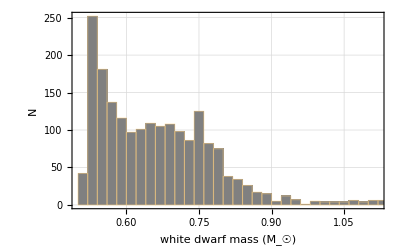

```mathematica
Histogram[DQcut,ChartStyle->{Gray},Frame->True,LabelStyle->{(FontFamily->"Times"), Black},FrameLabel-> {Style["white dwarf mass (M_☉)"],Style["N"]},BaseStyle->{FontSize->20},GridLines->Automatic]
```

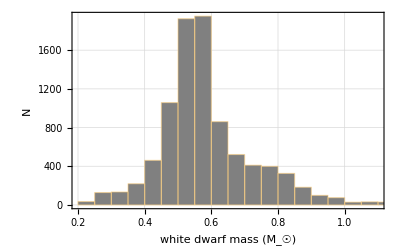

```mathematica
Histogram[DAcut,ChartStyle->{Gray},Frame->True,LabelStyle->{(FontFamily->"Times"), Black},FrameLabel-> {Style["white dwarf mass (M_☉)"],Style["N"]},BaseStyle->{FontSize->20},GridLines->Automatic]
```

The above histograms are just a reproduction of that is shown in Camisassa https://arxiv.org/abs/2305.02110 Fig 8., from Jiménez-Esteban et al. (2023).

A quick check for how many near Chandrasekhar white dwarfs in this sample :

```mathematica
Select[DAcut,#>1.3&]
```

{1.30079,1.30008,1.30984,1.59857,1.45316,1.65787}

```mathematica
Select[DQcut,#>1.3&]
```

{1.30377,1.35056}

There are 8.

Then for the total number of WD classified as DA vs DQ :

```mathematica
DA//Length
```

```mathematica
DQ//Length
```

### b. Generating binaries given the mass distribution in the 100pc sample

We want to assemble a big enough number, say ~ 10,000 white dwarf binaries whose components are drawn from the mass distribution of DA white dwarfs in the complete sample.

```mathematica
nWD=10000;
```

```mathematica
InvCDF[u_] = InverseCDF[HistogramDistribution[DAcut],u];
```

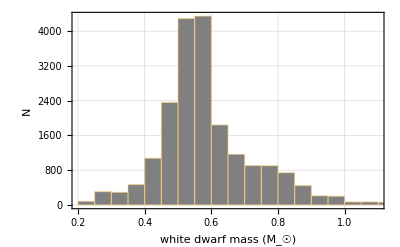

```mathematica
(*Generate uniform random draws and transform them*)
SeedRandom[];
drawtab = Table[InvCDF[RandomReal[]],2,{nWD}];
draws=drawtab[[1]];
draws2=drawtab[[2]];

(*Visualize the distribution of your draws*)
Histogram[Join[draws,draws2],ChartStyle->{Gray},Frame->True,LabelStyle->{(FontFamily->"Times"), Black},FrameLabel-> {Style["white dwarf mass (M_☉)"],Style["N"]},BaseStyle->{FontSize->20},GridLines->Automatic]
```

As expected, the draws follow the “DAcut” distribution which we based the sampling on.

Now we calculate the sum of the pairs of drawn masses :

```mathematica
Masssum = draws+draws2;
```

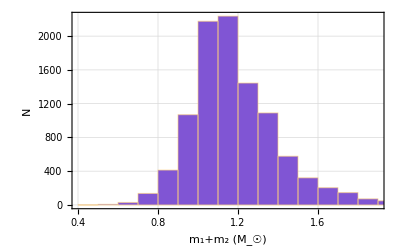

```mathematica
Histogram[Masssum,ChartStyle->{Blend[{Purple,Cyan,Magenta}]},Frame->True,LabelStyle->{(FontFamily->"Times"), Black},FrameLabel-> {Style["m_1+m_2 (M_☉)"],Style["N"]},BaseStyle->{FontSize->20},GridLines->Automatic]
```

The mean is:

```mathematica
Mean[Masssum]
```

1.18402

Now we only select our predicted sums in the range of 0.9 < M_☉< 1.4:

```mathematica
Sumcut = Select[Masssum,#>0.9&];
Sumcut2 = Select[Sumcut,#< 1.4&];
```

Assuming this random pairing of WDs according to the observed mass distribution, here is the mass distribution of “Ultra-massive” merger products that we predict:

#### Fig 1.

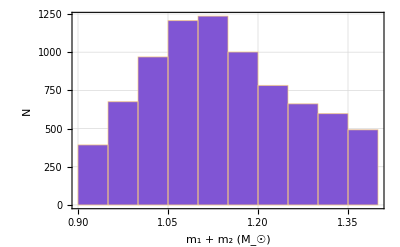

```mathematica
Histogram[Sumcut2,8,ChartStyle->{Blend[{Purple,Cyan,Magenta}]},Frame->True,LabelStyle->{(FontFamily->"Times"), Black},FrameLabel-> {Style["m_1 + m_2 (M_☉)"],Style["N"]},BaseStyle->{FontSize->20},GridLines->Automatic]
```

### c. The binary sample from Jewett

We want to compare this (naive?) prediction of a mass distribution to the mass distribution of the binary merger candidates . This could tell us about the rate of sub-Chandrasekar mergers which leave no remnant (e.g. in a Type Ia), i.e about a “disappeared” population of CO+CO mergers.

(Table here https://docs.google.com/spreadsheets/d/1zJ0aNjJhfFmAR0WJCnY4nyoMFPHAGY2Y2dkvxcnTkek/edit?usp=sharing)

```mathematica
Filenamebinary = "Jewett-binary-only-mass.dat";
binarymass=Select[NumericQ][Import[Filenamebinary,{"Data",All,1}]];
```

The total number of merger candidates in their Table 9. is :

```mathematica
binarymass//Length
```

99

We plot the mass distribution of all 99 binary merger candidates

#### Fig 2.

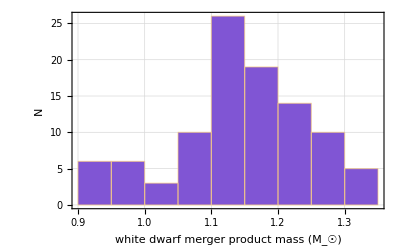

```mathematica
Histogram[binarymass,8,ChartStyle->{Blend[{Purple,Cyan,Magenta}]},Frame->True,LabelStyle->{(FontFamily->"Times"), Black},FrameLabel-> {Style["white dwarf merger product mass (M_☉)"],Style["N"]},BaseStyle->{FontSize->20},GridLines->Automatic]
```

The merger candidates in the observed population shares the same mean mass ~ 1.1M_☉, however it is much more sharply peaked there.
At least to the right of the peak in Fig 2., where the number reduces with M much more dramatically than the prediction in Fig 1., we may speculate that there is a missing population?

To the left.. is it possible that some weren’t picked up in the search? And is there a preference for more massive mergers leading to stronger fields / stronger rotation? Surely for rotation..

### Discussion : about Q branch

not all of these binary merger product candidates are on the Q branch, and conversely not all Q branch ultra - massive WD will be merger products . We may want to consider refining the sample ourselves?

# 2. Results : A merger rate from the population of post-merger ultra-massive WD candidates

Taking the merger candidates in Fig 2., we can approximate a galactic merger rate.
For this calculation, we will assume that the number of observed merger products “near” the Chandrasekhar limit is roughly representative of the number of CO+CO binaries which merged in the past. This is probably a very generous assumption, since exploding mergers should still be dominated by roughly Chandrasekhar sums (is this true?) but we will proceed to calculate a merger rate.

We take the number of the 99 merger candidates with mass greater than 1.2M_☉ (is this a good assumption?):

```mathematica
Nproduct100pc=Length[ Select[binarymass,#> 1.2&]]
```

29

There are 29.

Now for the detectable volume, we construct a sphere with radius 100 pc

```mathematica
VLr = 0.1;
```

In kpc, the volume is

```mathematica
v100pc = 4/3 π VLr^3;
```

While the volume of the Milky Way will have a diameter of 30 kpc and scale height 1 kpc (note I found some other paper which uses a smaller scale height):

```mathematica
vMW = π 15^2 1//N
```

706.858

So that the observable volume assumed to be populated ~ uniformly by WD is

```mathematica
vobs=v100pc/vMW//N
```

5.92593×10^-6

So there are 29 merger products near the Chandrasekar limit in the 100 pc sample, which is a volume ~ 10^-6 of the Milky Way. So the number of these merger products in the whole Milky Way should be

```mathematica
NproductMW = Nproduct100pc/vobs
```

4.89375×10^6

We now consider that they are only observable for up to ~ 7 Gyr, so that the total number to have ever existed in ~13 Gyr is roughly

```mathematica
NproductMW (13 Gyr)/(7 Gyr)
```

9.08839×10^6

Then, dividing by the age of the Milky Way ~ 13 Gyr, the average merger rate (in /year) should be

```mathematica
NproductMW (13 Gyr)/(7 Gyr)(13 10^9 year)^-1
```

0.000699107/year

```mathematica
RMWlow=NproductMW (13 Gyr)/(7 Gyr)(13 10^9)^-1
```

0.000699107

# 3. Results: Predictions for the number of double degenerate mergers exceeding 1.0M_☉ in the 100 pc sample

This calculation is a prediction for the number distribution of short period CO+CO binaries with merger timescales << Hubble time (i.e. < Gyr or so, orbital period < few hours.)

The number distribution relies on a constant merger rate, so is only applicable if the population is heading towards merger in < Gyr. In other words, for a population of binaries heading toward gravitational wave driven merger, the production rate = destruction rate (constant star formation rate) = “steady state”. This assumption is valid in the Milky Way over Myr timescales, but not over Gyr e.g. https://noirlab.edu/public/images/noao1903c/

This technique was first developed for binary black hole mergers (Kyutoku and Seto 2016) and later binary neutron stars (McNeill and Seto 2022). But it has more recently been applied to double white dwarfs (Seto 2023, McNeill and Hirai 2025)

Finally we compare this to the observed population of CO + CO binaries in this special short-period regime.
Currently there is ONE!

### Chirp mass distribution from 1b.

```mathematica
Mchirpf[m11_,m22_]=(m11 m22)^(3/5)/(m11+m22)^(1/5);
```

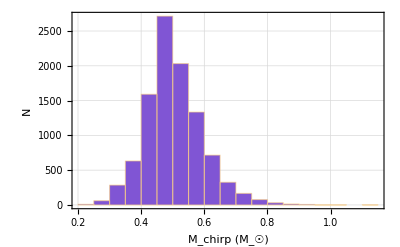

```mathematica
Histogram[Mchirpf[draws,draws2],ChartStyle->{Blend[{Purple,Cyan,Magenta}]},Frame->True,LabelStyle->{(FontFamily->"Times"), Black},FrameLabel-> {Style["M_chirp (M_☉)"],Style["N"]},BaseStyle->{FontSize->20},GridLines->Automatic]
```

We may want to roughly compare with the chirp mass distribution of CO+CO binaries in fig 4 here https://arxiv.org/html/2607.09980v1

```mathematica
mchirpav = Mean[Mchirpf[draws,draws2]]
```

0.504518

To proceed (and make the calculation later easier), it should be reasonable to say that the chirp mass of merging binaries is "sharply peaked at 0.5 M_☉"

But we should note that the chirp mass of a Chandrasekhar limit merger is slightly larger, at

```mathematica
Mchirpf[0.7,0.7]
```

0.609385

### Calculating the total number of short period CO+CO binaries (i.e. the progenitors of Ultra-massive WD merger products) in the 100 pc sample

We first define the rate of decay for a given binary due to the emission of gravitational waves

```mathematica
dfdt[fGW_,mchirp_]=(96 π^(8/3)(6.67 10^-8)^(5/3)(fGW)^(11/3)(mchirp 2 10^33)^(5/3))/(5 (3 10^10)^5)
```

5.82578×10^-7 fGW^(11/3) mchirp^(5/3)

The following calculation is only applicable for binaries which will merge in << Hubble time, so we solve for the critical orbital period where binaries will or won’t merge.

First define a "steady state" timescale to be 1 Gyr (in seconds)

```mathematica
Tsteady =1 10^9 π 10^7;
```

Then we calculate the merger timescale

```mathematica
Integrate[dfdt[fGW,0.5]^-1,{fGW,fmin,∞}]
```

ConditionalExpression[(2.04359×10^6)/fmin^(8/3), Im[fmin]≠0||Re[fmin]>0]

```mathematica
fmin/.Solve[(2.043589184607502*^6)/fmin^(8/3)==Tsteady,fmin][[1]]
```

0.000151344

In hours, this is 3.7 hours

So for the minimum frequency a 0.5M_☉ chirp mass binary needs at formation, to reach mass transfer in 1 Gyr (so that the steady state assumption is justified) is 0.151 mHz . We will limit our calculation to a minimum frequency of 0.000151344 Hz, and take the maximum to be ~ few mHz.. but note that the higher frequency is not so sensitive.

```mathematica
fGWlow=0.00015134441398294879;
fGWhigh=0.003;
```

Considering that CO + CO binaries are likely to be found by spectroscopy rather than eclipses (is this OK?), unlike McNeill and Hirai 2025 we do not include the eclipse probability in the selection effect function.

Taking the rate of orbital decay due to GW emission, assuming some constant merger rate we can predict the total number of short period binaries we expect in 100 pc. Taking the Type Ia rate to be 1 per year (0.01 / year)

```mathematica
RMWhigh=0.01;
```

this is

```mathematica
N100pcIa = RMWhigh/(π 10^7)vobs Integrate[dfdt[fGW,mchirpav]^-1,{fGW,fGWlow,fGWhigh}]
```

11.6714

Or taking the rate we predict from the merger product candidates, which was

```mathematica
RMWlow
```

this is

```mathematica
N100pcUltra = RMWlow/(π 10^7)vobs Integrate[dfdt[fGW,mchirpav]^-1,{fGW,fGWlow,fGWhigh}]
```

1.16714

In summary, taking the Ia rate as the merger rate predicts ~10, while our merger rate predicts ~1.

### Calculating a number distribution of CO+CO binaries (i.e. the progenitors of Ultra-massive WD merger products) in the 100 pc sample

We just calculated the total number via definite integral, but given a merger rate we can also predict the mass distribution . This is really only relevant if there are larger volume limited samples in the future, but we present it anyway .

For the number distribution with frequency N(f), we take the integral of the merger rate (Eq . 5 in McNeill and Seto 2022)

For taking the Ia rate, the number distribution as a function of mHz will be given by the integral

```mathematica
RMWhigh/(π 10^7)vobs Integrate[dfdt[0.001fGW,0.5]^-1,fGW]0.001
```

-0.0770957/fGW^(8/3)

```mathematica
NIa[2/(z 0.001 60 60)]
```

-0.0770957/fGW^(8/3)

```mathematica
NIa[f_]:=RMWhigh/(π 10^7)vobs Integrate[dfdt[0.001fGW,0.5]^-1,fGW]0.001
```

```mathematica
RMWhigh/(π 10^7)vobs Integrate[dfdt[0.001fGW,0.5]^-1,fGW]0.001
```

-0.0770957/fGW^(8/3)

We want to work with the orbital period instead, f_GW = 2/P_orb, so that the distribution is given by

```mathematica
periodIa=ProbabilityDistribution[-NIa[fGW] fGW^(8/3)(2/(z 0.001 60 60))^(-8/3),{z,fGWlow,Infinity}];
PeriodIa[P_]:= PDF[periodIa,P];
```

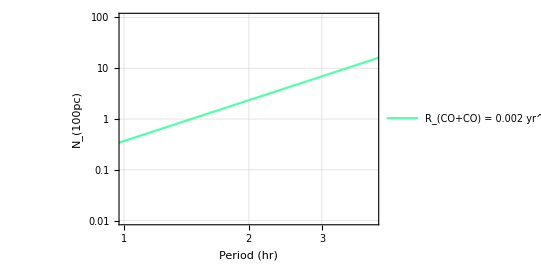

```mathematica
LogLogPlot[{PeriodIa[z]},{z,0.2,10},AspectRatio->2/3,Frame->True,LabelStyle->{(FontFamily->"Times"), Black},FrameLabel-> {Style["Period (hr)"],Style["N_(100pc)"]},BaseStyle->{FontSize->20},GridLines->Automatic,PlotStyle-> { {Blend[{Cyan,Green,White}]},{ Blend[{Magenta,Cyan,Magenta}]}},PlotRange->{{1,4},{0.01,100}},FrameTicks->{{Automatic,Nint},{Automatic,Automatic}},FrameTicksStyle->{{Black,Gray},{Black,Black}},PlotLegends->{Style["R_(CO+CO) = 0.002 yr^-1(Type Ia) → N_(100pc) = 8",18,Black],Style["R_(CO + CO) = 2 × 10^-4 yr^-1(Q branch) → N_(100pc) = 0.8",18,Black]}]
```

Then taking the lower rate,

```mathematica
periodUltra=ProbabilityDistribution[-RMWlow/RMWhigh NIa[fGW] fGW^(8/3)(2/(z 0.001 60 60))^(-8/3),{z,fGWlow,Infinity}];
```

#### Fig 4.

```mathematica
PeriodUltra[P_]:=PDF[periodUltra,P];
```

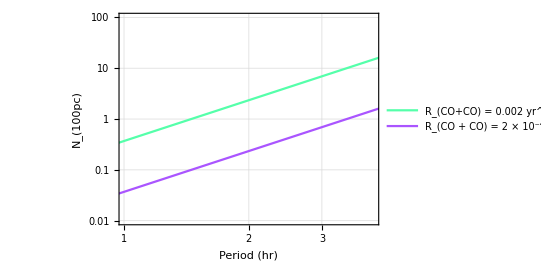

```mathematica
LogLogPlot[{PeriodIa[z],PeriodUltra[z]},{z,0.2,10},AspectRatio->2/3,Frame->True,LabelStyle->{(FontFamily->"Times"), Black},FrameLabel-> {Style["Period (hr)"],Style["N_(100pc)"]},BaseStyle->{FontSize->20},GridLines->Automatic,PlotStyle-> { {Blend[{Cyan,Green,White}]},{ Blend[{Magenta,Cyan,Magenta}]}},PlotRange->{{1,4},{0.01,100}},FrameTicks->{{Automatic,Nint},{Automatic,Automatic}},FrameTicksStyle->{{Black,Gray},{Black,Black}},PlotLegends->{Style["R_(CO+CO) = 0.002 yr^-1(Type Ia) → N_(100pc) ~ 10",18,Black],Style["R_(CO + CO) = 2 × 10^-4 yr^-1(merger products) → N_(100pc) ~ 1",18,Black]}]
```

### Discussion : about the number of binaries in 100 pc

Currently there is this ONE reported binary. A key discussion point is whether all short period binaries have been identified in the 100 pc sample.
We might need to consider limiting magnitudes etc.

## References

Burdge, K. B., Prince, T. A., Fuller, J., et al. 2020, ApJ,905, 32

Brown, W. R., Kilic, M., Hermes, J. J., et al. 2011, ApJL, 737, L23

Brown, W. R., Kilic, M., Kenyon, S. J., & Gianninas, A. 2016, ApJ, 824, 46

Kilic, M., Brown, W. R., Heinke, C. O., et al. 2016, MNRAS, 460, 4176

Kupfer & Korol, Littenberg, T. B., Shah, S., et al. 2024, ApJ, 963, 100,